```mathematica
(*Reissner-Nordstrom AdS q≤qcrit case*)
```

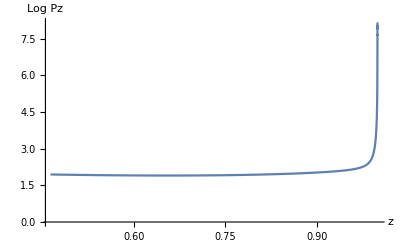

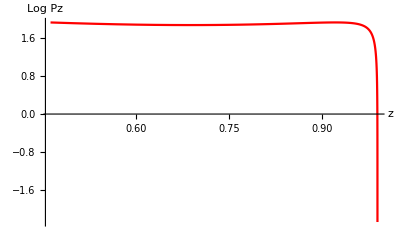

```mathematica
Block[
{qcrit,zm,zm1,t,fz,pz,B,C1,A},
fz[zh_,μ_,z_]:=1-(1+zh^2μ^2)(z/zh)^3+zh^2μ^2(z/zh)^4;
qcrit[μ_,zh_,zs_]:=zh Sqrt[1-(1+zh^2 μ^2)(zs/zh)^3+zh^2μ^2(zs/zh)^4]/μ/zs/(zh-zs);
zm1[q1_,μ1_,zh1_,zs1_]:=NDSolveValue[
{-(q μ)/zh-(zh^3 z[t] (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+z'[t]^2/(z[t]^2 (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))-(z[t] (-3 (1+zh^2 μ^2)+4 zh μ^2 z[t]-(zh^6 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)))/(2 zh^3 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(√(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/z[t]^2-z''[t]/((z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(z'[t]^2 (-(3 (1+zh^2 μ^2) z[t]^2)/zh^3+(4 μ^2 z[t]^3)/zh^2-(zh^3 z[t]^2 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)-(2 z''[t])/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/(2 (z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2))^(3/2))==0/.{μ->μ1,zh->zh1,q->q1},z[0]==zs1,z'[0]==0},z,{t,0.01,8.5}
];
zm[t1_,q1_,μ1_,zh1_,zs1_]:=zm1[q1,μ1,zh1,zs1][t1];
pz[t1_,q1_,μ1_,zh1_,zs1_]:=1/zm[t1,q1,μ1,zh1,zs1]/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})/Sqrt[fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]-1/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})^2];
Print[ListLinePlot[Table[{zm[i,0.99*qcrit[1.3,1,0.1],1.3,1,0.1],pz[i,0.99*qcrit[1.3,1,0.1],1.3,1,0.1]//Log},{i,0.5,8.5,0.05}],AxesLabel->{z,Log Pz},PlotRange->All]];
Print[ListLinePlot[Table[{zm[i,1.00*qcrit[1.3,1,0.1],1.3,1,0.1],pz[i,1.00*qcrit[1.3,1,0.1],1.3,1,0.1]//Log},{i,0.5,8.5,0.05}],AxesLabel->{z,Log Pz},PlotRange->All,PlotStyle->Red]];
]
```

```mathematica
(*Reissner-Nordstrom AdS q>qcrit case*)
```

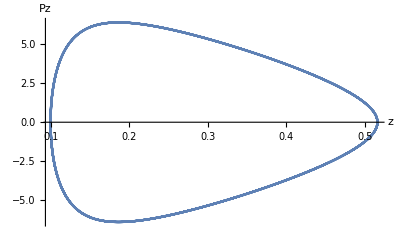

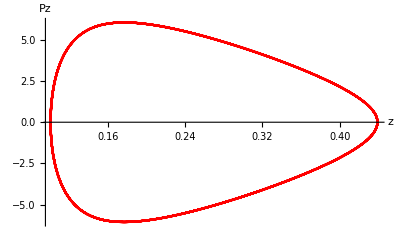

```mathematica
Block[
{qcrit,zm,zm1,t,fz,pz,B,C1,A},
fz[zh_,μ_,z_]:=1-(1+zh^2μ^2)(z/zh)^3+zh^2μ^2(z/zh)^4;
qcrit[μ_,zh_,zs_]:=zh Sqrt[1-(1+zh^2 μ^2)(zs/zh)^3+zh^2μ^2(zs/zh)^4]/μ/zs/(zh-zs);
zm1[q1_,μ1_,zh1_,zs1_]:=NDSolveValue[
{-(q μ)/zh-(zh^3 z[t] (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+z'[t]^2/(z[t]^2 (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))-(z[t] (-3 (1+zh^2 μ^2)+4 zh μ^2 z[t]-(zh^6 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)))/(2 zh^3 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(√(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/z[t]^2-z''[t]/((z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(z'[t]^2 (-(3 (1+zh^2 μ^2) z[t]^2)/zh^3+(4 μ^2 z[t]^3)/zh^2-(zh^3 z[t]^2 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)-(2 z''[t])/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/(2 (z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2))^(3/2))==0/.{μ->μ1,zh->zh1,q->q1},z[0]==zs1,z'[0]==0},z,{t,0.01,8.5}
];
zm[t1_,q1_,μ1_,zh1_,zs1_]:=zm1[q1,μ1,zh1,zs1][t1];
pz[t1_,q1_,μ1_,zh1_,zs1_]:=1/zm[t1,q1,μ1,zh1,zs1]/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})/Sqrt[fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]-1/fz[zh1,μ1,zm[t1,q1,μ1,zh1,zs1]]*(D[zm1[q1,μ1,zh1,zs1][t],t]/.{t->t1})^2];
Print[ListLinePlot[Table[{zm[i,1.8*qcrit[1.3,1,0.1],1.3,1,0.1],pz[i,1.8*qcrit[1.3,1,0.1],1.3,1,0.1]},{i,0.5,8.5,0.01}],AxesLabel->{z,Pz},PlotRange->All]];
Print[ListLinePlot[Table[{zm[i,2.1*qcrit[1.3,1,0.1],1.3,1,0.1],pz[i,2.1*qcrit[1.3,1,0.1],1.3,1,0.1]},{i,0.5,8.5,0.01}],AxesLabel->{z,Pz},PlotRange->All,PlotStyle->Red]];
]
```

```mathematica
(*Gauss-Bonnet AdS q≤qcrit case*)
```

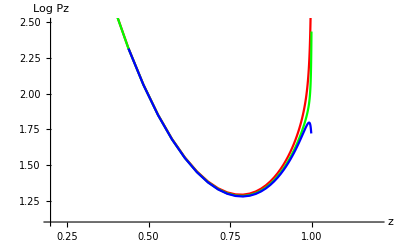

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
dfz1[t_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=D[fz1[t1,q1,zp1,zs1,μ1,l1,λ1],t1]/.{t1->t};
pz[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=Block[
{zd,z2,fz,n1,β},
z2=fz1[t1,q1,zp1,zs1,μ1,l1,λ1];
fz=f[z2,1/zp1,μ1,l1,λ1,Sqrt[8Pi]];
β=1/(D[f[zw,1/zp1,μ1,l1,λ1,Sqrt[8Pi]],zw]/.{zw-> z2});
zd=dfz1[t1,q1,zp1,zs1,μ1,l1,λ1];
n1=Sqrt[(1+Sqrt[1-4λ1])/2];
Return[β/z2/fz zd/Sqrt[n1^2fz-zd^2/fz]];
];
Show[
ListLinePlot[Table[{fz1[i,0.9qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.11],1,0.11,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.11],1,0.11]//Abs,pz[i,0.9qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.11],1,0.11,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.11],1,0.11]//Abs//Log},{i,0.01,4,0.05}],PlotStyle->Red],
ListLinePlot[Table[{fz1[i,0.905qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.11],1,0.11,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.11],1,0.11]//Abs,pz[i,0.905qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.11],1,0.11,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.11],1,0.11]//Abs//Log},{i,0.01,4,0.05}],PlotStyle->Green],
ListLinePlot[Table[{fz1[i,0.9069qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.11],1,0.11,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.11],1,0.11]//Abs,pz[i,0.9069qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.11],1,0.11,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.11],1,0.11]//Abs//Log},{i,0.01,4,0.05}],PlotStyle->Blue],
PlotRange->{{0.2,1.2},{1.1,2.5}},AxesOrigin->{0.2,1.1},AxesLabel->{z,Log Pz}
]
]
```

```mathematica
(*Gauss-Bonnet AdS q>qcrit case*)
```

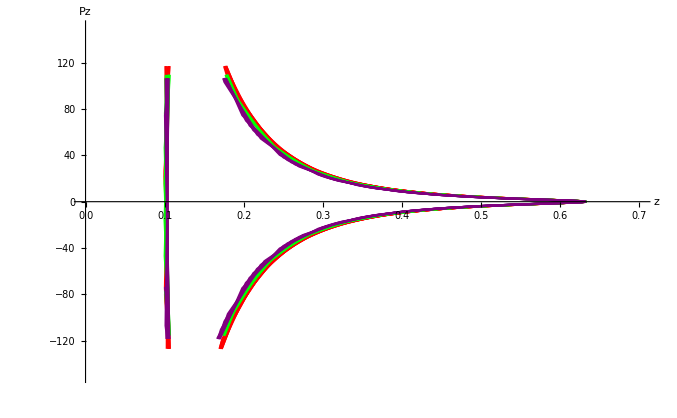

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_,k_]:=k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_,k_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ,k]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_,k_]:=Sqrt[f[zs,1/zp,μ,l,λ,k]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q2 μ z[t])/zp^2+(2 l^2 λ z'[t]^2)/(z[t]^2 (1-√(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))+1/z[t]^2(√(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(24 √6 l^2 λ z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^2)/(zp^4 √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))-(√6 z[t]^2 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) (-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))-12 l^4 λ^2 z'[t]^2)))/(l^2 zp^8 λ √(1/zp^4(3 zp^4 (1-4 λ)+4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2 √((-2 λ (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2) z[t]^4+8 k^2 l^2 λ μ^2 z[t]^6+zp^4 ((1+√(1-4 λ)) (-3+6 λ+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+12 l^4 λ^2 z'[t]^2))/(l^2 zp^4 λ (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))))))+(6 l^2 λ z''[t])/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) √(-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))-(3 l^2 λ z'[t] (-(2 z[t]^3 (3+3 √(1-4 λ)+32 l^2 π zp^2 μ^2-6 k^2 l^2 μ^2 z[t]^2) z'[t])/(l^2 zp^4 √((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))-(24 l^2 λ z[t]^3 (6 λ-16 l^2 π zp^2 (-1+√(1-4 λ)) μ^2+3 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^2) z'[t]^3)/(zp^4 √(1-4 λ+(4 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4)/(3 zp^4)+(4 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/(3 zp^4)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))^2)+(12 l^2 λ z'[t] z''[t])/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4))))/(z[t] (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6))) (-1/(12 l^2 λ)(1+√(1-4 λ)) (-3+√(1/zp^4(9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)))+(6 l^2 λ z'[t]^2)/(-3+√((9 zp^4 (1-4 λ)+12 (3 λ-8 l^2 π zp^2 (-1+√(1-4 λ)) μ^2) z[t]^4+12 k^2 l^2 (-1+√(1-4 λ)) μ^2 z[t]^6)/zp^4)))^(3/2))==0/.{k->Sqrt[8Pi],q2->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,9}
];
μextreme[k_,l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/k/l/zh;
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
dfz1[t_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=D[fz1[t1,q1,zp1,zs1,μ1,l1,λ1],t1]/.{t1->t};
pz[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=Block[
{zd,z2,fz,n1,β},
z2=fz1[t1,q1,zp1,zs1,μ1,l1,λ1];
fz=f[z2,1/zp1,μ1,l1,λ1,Sqrt[8Pi]];
β=1/(D[f[zw,1/zp1,μ1,l1,λ1,Sqrt[8Pi]],zw]/.{zw-> z2});
zd=dfz1[t1,q1,zp1,zs1,μ1,l1,λ1];
n1=Sqrt[(1+Sqrt[1-4λ1])/2];
Return[β/z2/fz zd/Sqrt[n1^2fz-zd^2/fz]];
];
Show[
ListLinePlot[Table[{Abs[fz1[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.12],1,0.12,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.12],1,0.12]],Re[pz[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.12],1,0.12,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.12],1,0.12]]},{i,0.01,9,0.05}],PlotStyle->Red],
ListLinePlot[Table[{Abs[fz1[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.13],1,0.13,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.13],1,0.13]],Re[pz[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.13],1,0.13,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.13],1,0.13]]},{i,0.01,9,0.05}],PlotStyle->Green],
ListLinePlot[Table[{Abs[fz1[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.14],1,0.14,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.14],1,0.14]],Re[pz[i,2qcrit[0.1,1,0.75μextreme[Sqrt[8Pi],1,1,0.14],1,0.14,Sqrt[8Pi]],1,0.1,0.75μextreme[Sqrt[8Pi],1,1,0.14],1,0.14]]},{i,0.01,9,0.05}],PlotStyle->Purple],PlotRange->{{0,0.7},{-150,150}},
AxesOrigin->{0,0},AxesLabel->{z,Pz}
]
]
```

```mathematica
(*Born-Infeld AdS q≤qcrit case part 1*)
```

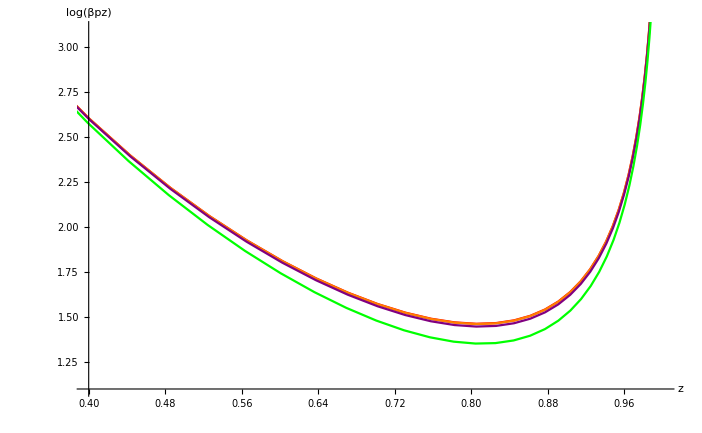

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz,βpz},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
zm1[q1_,zs1_,β1_,γ1_,μ1_]:=NDSolveValue[
{-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0/.{q->q1,β->β1,γ->γ1,μ->μ1},z[0]== zs1,z'[0]==0},z,{t,0.01,4}
];
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
fz1[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=zm1[q1,zs1,β1,γ1,μ1][t1];
dfz1[t_,q1_,zs1_,β1_,γ1_,μ1_]:=D[fz1[t1,q1,zs1,β1,γ1,μ1],t1]/.{t1->t};
pz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
Return[1/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
βpz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz,β,n1,zw},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
β=1/(D[f[zw,β1,γ1,μ1],zw]/.{zw-> z2});
Return[β/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
Print[Show[
ListLinePlot[Table[{Abs[fz1[i,0.8qcrit[0.1,0,0.001,2/Sqrt[3] ],0.1,0,0.001,2/Sqrt[3] ]],Abs[βpz[i,0.8qcrit[0.1,0,0.001,2/Sqrt[3] ],0.1,0,0.001,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Red],
ListLinePlot[Table[{Abs[fz1[i,0.8qcrit[0.1,0,0.01,2/Sqrt[3] ],0.1,0,0.01,2/Sqrt[3] ]],Abs[βpz[i,0.8qcrit[0.1,0,0.01,2/Sqrt[3] ],0.1,0,0.01,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{Abs[fz1[i,0.8qcrit[0.1,0,0.1,2/Sqrt[3] ],0.1,0,0.1,2/Sqrt[3] ]],Abs[βpz[i,0.8qcrit[0.1,0,0.1,2/Sqrt[3] ],0.1,0,0.1,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Purple],
ListLinePlot[Table[{Abs[fz1[i,0.8qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]],Abs[βpz[i,0.8qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]]//Log},{i,0.01,3,0.05}],PlotStyle->Green],
PlotRange->{{0.4,1},{1.1,3.1}},AxesOrigin->{0.4,1.1},AxesLabel->{z,Log[βpz]}
]];
]
```

```mathematica
(*Born-Infeld AdS q≤qcrit case part 2*)
```

NDSolveValue::ntdv: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

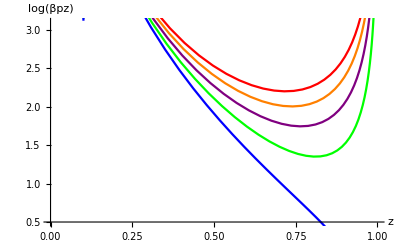

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz,βpz},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
zm1[q1_,zs1_,β1_,γ1_,μ1_]:=NDSolveValue[
{-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0/.{q->q1,β->β1,γ->γ1,μ->μ1},z[0]== zs1,z'[0]==0},z,{t,0.01,4}
];
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
fz1[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=zm1[q1,zs1,β1,γ1,μ1][t1];
dfz1[t_,q1_,zs1_,β1_,γ1_,μ1_]:=D[fz1[t1,q1,zs1,β1,γ1,μ1],t1]/.{t1->t};
pz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
Return[1/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
βpz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz,β,n1,zw},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
β=1/(D[f[zw,β1,γ1,μ1],zw]/.{zw-> z2});
Return[β/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
Print[Show[
ListLinePlot[Table[{Abs[fz1[i,0.2qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]],Abs[βpz[i,0.2qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]]//Log},{i,0.01,3,0.05}],PlotStyle->Red],
ListLinePlot[Table[{Abs[fz1[i,0.4qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]],Abs[βpz[i,0.4qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]]//Log},{i,0.01,3,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{Abs[fz1[i,0.6qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]],Abs[βpz[i,0.6qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]]//Log},{i,0.01,3,0.05}],PlotStyle->Purple],
ListLinePlot[Table[{Abs[fz1[i,0.8qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]],Abs[βpz[i,0.8qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]]//Log},{i,0.01,3,0.05}],PlotStyle->Green],
ListLinePlot[Table[{Abs[fz1[i,1.0qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]],Abs[βpz[i,1.0qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]]//Log},{i,0.01,3,0.05}],PlotStyle->Blue],
PlotRange->{{0,1},{0.5,3.1}},AxesOrigin->{0,0.5},AxesLabel->{z,Log[βpz]}
]];
]
```

```mathematica
(*Born-Infeld AdS q>qcrit case*)
```

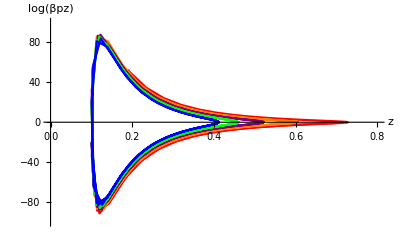

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz,βpz},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
zm1[q1_,zs1_,β1_,γ1_,μ1_]:=NDSolveValue[
{-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0/.{q->q1,β->β1,γ->γ1,μ->μ1},z[0]== zs1,z'[0]==0},z,{t,0.01,4}
];
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
fz1[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=zm1[q1,zs1,β1,γ1,μ1][t1];
dfz1[t_,q1_,zs1_,β1_,γ1_,μ1_]:=D[fz1[t1,q1,zs1,β1,γ1,μ1],t1]/.{t1->t};
pz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
Return[1/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
βpz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz,β,n1,zw},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
β=1/(D[f[zw,β1,γ1,μ1],zw]/.{zw-> z2});
Return[β/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
Print[Show[
ListLinePlot[Table[{Abs[fz1[i,1.2qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]],Re[βpz[i,1.2qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]]},{i,0.01,3,0.05}],PlotStyle->Red],
ListLinePlot[Table[{Abs[fz1[i,1.4qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]],Re[βpz[i,1.4qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]]},{i,0.01,3,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{Abs[fz1[i,1.6qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]],Re[βpz[i,1.6qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]]},{i,0.01,3,0.05}],PlotStyle->Purple],
ListLinePlot[Table[{Abs[fz1[i,1.8qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]],Re[βpz[i,1.8qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]]},{i,0.01,3,0.05}],PlotStyle->Green],
ListLinePlot[Table[{Abs[fz1[i,2.0qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]],Re[βpz[i,2.0qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]]},{i,0.01,3,0.05}],PlotStyle->Blue],
PlotRange->{{0,0.8},{-100,100}},AxesOrigin->{0,0},AxesLabel->{z,Log[βpz]}
]];
]
```

```mathematica
(* Hyperscale violating Einstein-dilaton-Maxwell black hole case - only the q<qcrit case*)
(* We did not plot the q≥qcrit as we did not want to repeat the routine analysis. *)
```

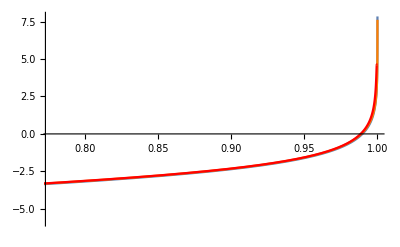

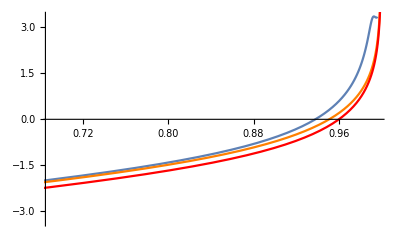

```mathematica
Block[
{μextreme, qcrit,uz1,fu1,dfu1,βpu},
μextreme[uh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]/uh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
qcrit[us_,uh_,μ_,z_,θ_]:=us^(θ/2-z)Sqrt[1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z))]/(μ(1-(us/uh)^(z-θ)));
uz1[q_,us_,uh_,μ_,z_,θ_]:=NDSolveValue[
{-(q (z-θ) μ (u[t]/uh)^(z-θ))/u[t]-((-2+θ) u[t]^(-2+θ/2) u'[t]^2)/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(θ/2) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-(u[t]^(-1+θ/2) (((-2-z+θ) u[t]^(3-2 z) (u[t]/uh)^(z-θ))/uh^2-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(3-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(3-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)+(2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))+((-((2+z-θ) (u[t]/uh)^(1+z-θ))/uh-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(1+2 z-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(1+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)) u'[t]^2)/(-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2))/(2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-1/2 (-2+θ) u[t]^(-2+θ/2) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))-(u[t]^(-1+θ/2) u''[t])/((1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(-1+θ/2) u'[t] ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) u'[t]+1/(2 uh^2 (2-θ))u[t]^(3-2 z) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^3)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)-(2 u'[t] u''[t])/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) (u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))^(3/2))==0,u[0]== us,u'[0]==0},u,{t,0.1,5.7}
];
fu1[t_,q_,us_,uh_,μ_,z_,θ_]:=uz1[q,us,uh,μ,z,θ][t];
dfu1[t_,q_,us_,uh_,μ_,z_,θ_]:=D[uz1[q,us,uh,μ,z,θ][t1],t1]/.{t1->t};
βpu[t_,q_,us_,uh_,μ_,z_,θ_]:=Block[
{du,u,fu,β},
du=dfu1[t,q,us,uh,μ,z,θ];
u=fu1[t,q,us,uh,μ,z,θ];
fu=1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z));
β=1/(D[1-(u1/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) u1^(2(z-θ+1))/uh^(2z-2θ)(1-(u1/uh)^(θ-z)),u1]/.{u1-> us});
Return[β u^(θ/2-1)du/(fu Sqrt[u^(2(1-z))fu - du^2/fu])];
];
Print[Show[
ListLinePlot[Table[{Abs[fu1[i,20,0.1,1,0.75μextreme[1,1.5,0.1800],1.5,0.1800]],-(Abs[βpu[i,20,0.1,1,0.75μextreme[1,1.5,0.1800],1.5,0.1800]]//Log)},{i,0.1,5,0.05}]],
ListLinePlot[Table[{Abs[fu1[i,20,0.1,1,0.75μextreme[1,1.5,0.1950],1.5,0.1950]],-(Abs[βpu[i,20,0.1,1,0.75μextreme[1,1.5,0.1950],1.5,0.1950]]//Log)},{i,0.1,5,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{Abs[fu1[i,20,0.1,1,0.75μextreme[1,1.5,0.1991],1.5,0.1991]],-(Abs[βpu[i,20,0.1,1,0.75μextreme[1,1.5,0.1991],1.5,0.1991]]//Log)},{i,0.1,5,0.05}],PlotStyle->Red]
]];
Print[Show[
ListLinePlot[Table[{Abs[fu1[i,10,0.1,1,0.75μextreme[1,1.5389,1.0],1.5389,1.0]],-(Abs[βpu[i,10,0.1,1,0.75μextreme[1,1.5389,1.0],1.5389,1.0]]//Log)},{i,0.1,5,0.05}]],
ListLinePlot[Table[{Abs[fu1[i,10,0.1,1,0.75μextreme[1,1.55,1.0],1.55,1.0]],-(Abs[βpu[i,10,0.1,1,0.75μextreme[1,1.55,1.0],1.55,1.0]]//Log)},{i,0.1,5,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{Abs[fu1[i,10,0.1,1,0.75μextreme[1,1.60,1.0],1.60,1.0]],-(Abs[βpu[i,10,0.1,1,0.75μextreme[1,1.60,1.0],1.60,1.0]]//Log)},{i,0.1,5,0.05}],PlotStyle->Red]
]];
]
```